### Reproducing the Zabusky & Kruskal KdV simulation (1965)

```mathematica
ZabuskyKruskalKdV = NDSolveValue[
    {D[u[t, x], {t}] + u[t, x]*D[u[t, x], {x}] + 
       D[u[t, x], {x, 3}] == 0, u[0, x] == Cos[Pi*x], 
     u[t, 0] == u[t, 2], (D[u[t, x], {x}] /. x -> 0) == 
      (D[u[t, x], {x}] /. x -> 2), (D[u[t, x], {x}, {x}] /. x -> 0) == 
      (D[u[t, x], {x}, {x}] /. x -> 2)}, u, {t, 0, 3.6/Pi}, {x, 0, 2}, 
    Method -> {"PDEDiscretization" -> {"MethodOfLines", 
        "SpatialDiscretization" -> {"TensorProductGrid", 
          "MinPoints" -> 1000}}}];
```

```mathematica
Plot3D[ZabuskyKruskalKdV[t,x],{t,0,3.6/π},{x,0,2},PlotPoints->50,AxesLabel->{t,x,u}]
```

-Graphics3D-

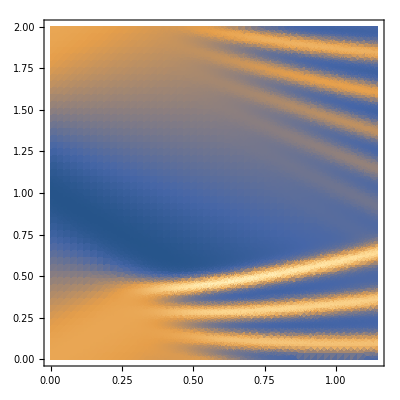

```mathematica
DensityPlot[ZabuskyKruskalKdV[t,x],{t,0,3.6/π},{x,0,2},PlotPoints->50]
```

```mathematica
Manipulate[Plot[ZabuskyKruskalKdV[t,x],{x,0,2}],{t,0,3.6/π}]
```